```mathematica
data=Import["/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/data/tiingo_btc.csv"];
```

```mathematica
data=data[[;;,2;;]];
data2=Select[data, StringContainsQ[#[[1]], "23:00"]&];
dates=DateObject[StringReplace[StringSplit[#1, "+"][[1]], "T"->" "], TimeZone->"UTC"]&/@data2[[;;,1]];
data3=Prepend[data2ᵀ[[2;;]], dates]ᵀ;
data4=Prepend[data3, data[[1]]];
```

```mathematica
btc=data4;
```

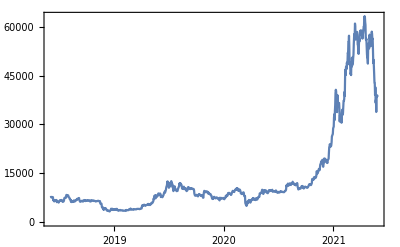

```mathematica
DateListPlot[btc[[2;;,1;;2]],PlotRange->All]
```

```mathematica
data=Import["/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/data/btc future and reference rate/btc_future_brr.csv"];
```

```mathematica
data=data[[;;,2;;3]];
data2=Select[data, #[[2]]≠""&][[2;;]];
dates=DateObject[{#, {"Month", "Day", "Year"}}]&/@data2[[;;,1]];
data3=Prepend[data2ᵀ[[2;;]], dates]ᵀ;
data4=Prepend[data3, {"date", "price"}];
```

```mathematica
fut=data4;
```

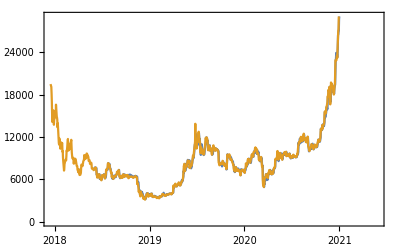

```mathematica
DateListPlot[{btc[[2;;,1;;2]],fut[[2;;]]}]
```

```mathematica
btc[[2;;5,1;;2]]
```

(Fri 1 Jun 2018 23:00:00UTC | 7514.07
Sat 2 Jun 2018 23:00:00UTC | 7629.14
Sun 3 Jun 2018 23:00:00UTC | 7710.39
Mon 4 Jun 2018 23:00:00UTC | 7502.92)

```mathematica
fut[[-5;;]]
```

(Thu 21 Dec 2017 00:00:00GMT+2 | 15330
Wed 20 Dec 2017 00:00:00GMT+2 | 17040
Tue 19 Dec 2017 00:00:00GMT+2 | 18200
Mon 18 Dec 2017 00:00:00GMT+2 | 19100
Fri 15 Dec 2017 00:00:00GMT+2 | 19500)

```mathematica
DateSelect[fut[[-5,1]]]
```

Thu 21 Dec 2017 00:00:00

```mathematica
Select[btc[[;;,1]],
```